# Capstone - Derangements

## John Knowles

### Exercise 1.

```mathematica
Clear["Global`*"]
{$RecursionLimit=6000};
```

```mathematica
NumFixedPoints[p_List]:=Count[p-Range[Length@p],0]
NumFixedPoints[{1,2,3,6,5,4,8,7}]
```

4

```mathematica
GetPermutationsByFixedPoints[n_Integer,k_Integer]:=Select[Permutations[Range[n]],k==Count[#-Range[n],0]&]
GetPermutationsByFixedPoints[5,0]//Short
Length@GetPermutationsByFixedPoints[5,0]
```

{{2,1,4,5,3},{2,1,5,3,4},{2,3,1,5,4},«38»,{5,4,1,3,2},{5,4,2,1,3},{5,4,2,3,1}}

44

```mathematica
Rest@ParallelTable[GetPermutationsByFixedPoints[i,0],{i,1,9}];
```

```mathematica
(*#/.x_:>NestWhile[RandomSample[#,Length@#]&,#,Not@FreeQ[#-x,0‌​]&]&; *)
```

### Exercise 2.

```mathematica
Length@GetPermutationsByFixedPoints[4,0]
```

9

```mathematica
Table[Length@GetPermutationsByFixedPoints[i,0],{i,1,9}]
```

{0,1,2,9,44,265,1854,14833,133496}

```mathematica
(* Subfactorial or rencontres numbers,or derangements:number of permutations of n elements with no fixed points. Euler Recurrance.*)
```

```mathematica
Timing@ParallelTable[RandomChoice[GetPermutationsByFixedPoints[9,0]],1]
```

{0.,{{8,6,2,1,4,7,3,9,5}}}

```mathematica
randChoices=ParallelTable[RandomChoice[Permutations[Range[9]]],100];
```

```mathematica
N@(Total@(NumFixedPoints/@randChoices)/100)
```

0.96

### Exercise 3.

```mathematica
Clear[GetSum,f]
GetSum[n_Integer]:=Sum[(-1)^i n!/i!,{i,0,n}]
GetSum/@Range[9]
f[0]=1;
f[n_]:=f[n]=n f[n-1]+(-1)^n
f/@Range[9]
```

{0,1,2,9,44,265,1854,14833,133496}

{0,1,2,9,44,265,1854,14833,133496}

```mathematica
(* Both of these functions produce the same output for all n, which is also the same for Derangement[9] and the deRngmt Function in exercise 5.*)
```

### Exercise 4.

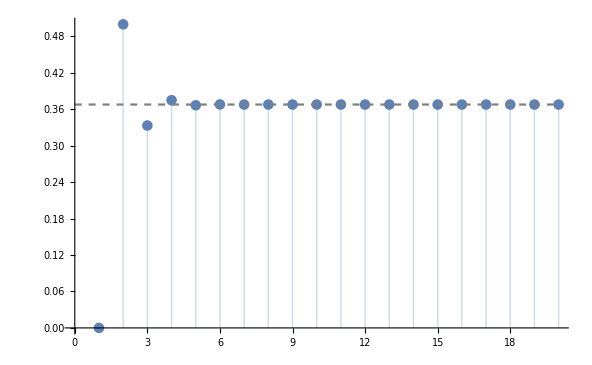

```mathematica
Show[ListPlot[ParallelTable[f[i]/i!,{i,1,20}],PlotRange->{0,1/2},Filling->Axis],Plot[1/E,{x,0,20},PlotStyle->{Dashed,Gray}]]
```

```mathematica
(* Converges to ~36% or 1/e *)
```

### Exercise 5.

```mathematica
Clear[deRngmt]
deRngmt[0]:=1;deRngmt[1]:=0;
deRngmt[n_Integer]:=deRngmt[n]=(n-1)(deRngmt[n-1]+deRngmt[n-2])
deRngmt[5]
deRngmt/@Range[20]
```

44

{0,1,2,9,44,265,1854,14833,133496,1334961,14684570,176214841,2290792932,32071101049,481066515734,7697064251745,130850092279664,2355301661033953,44750731559645106,895014631192902121}

```mathematica
(*
Counts[Flatten[Trace[deRngmt[9],deRngmt[_]]]];
Most@DownValues[deRngmt];
Dimensions/@Join[{GetPermutationsByFixedPoints[5,0],GetPermutationsByFixedPoints[4,0],GetPermutationsByFixedPoints[3,0],GetPermutationsByFixedPoints[2,0]}];
*)
```

```mathematica
DSolveValue[{(1-t)F'[t]==t F[t],F[0]==1},F[t],t]
f[t_]:=DSolveValue[{(1-t)F'[t]==t F[t],F[0]==1},F[t],t]
g=Sum[deRngmt[n]*(t^n/n!),{n,1,9}]
```

-ⅇ^-t/(-1+t)

t^2/2+t^3/3+(3 t^4)/8+(11 t^5)/30+(53 t^6)/144+(103 t^7)/280+(2119 t^8)/5760+(16687 t^9)/45360

```mathematica
Range[9]! Rest[CoefficientList[g,t]]
%==deRngmt/@Range[9]
```

{0,1,2,9,44,265,1854,14833,133496}

True

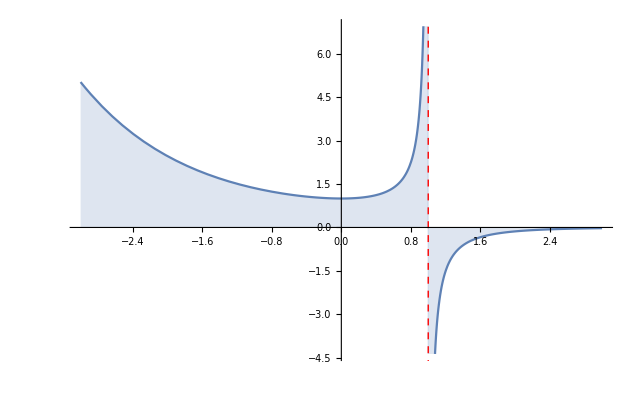

```mathematica
Show[Plot[Evaluate[DSolveValue[{(1-t)F'[t]==t F[t],F[0]==1},F[t],t],{t,-3,3}],Filling->Axis],Graphics[{Thick,Dashed,Red,Line[{{1,10},{1,-10}}]}]]
```

```mathematica
(*Plot[Evaluate[DSolveValue[{(1-t)F'[t]==t F[t],F[0]==1},F[t],t]],{t,-3,3},Filling->Axis,Exclusions->{t-1==0},ExclusionsStyle->Directive[Dashed,Red]]*)
```

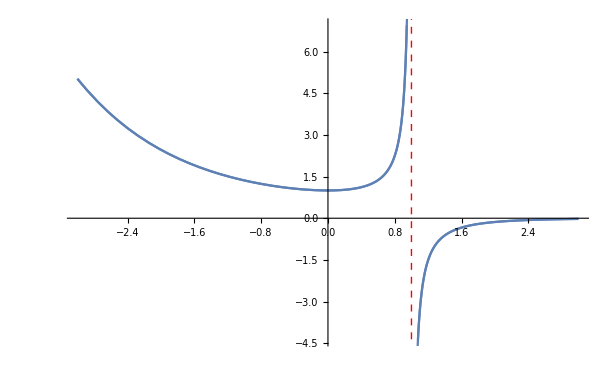

```mathematica
Show[Plot[Evaluate[DSolveValue[{(1-t)F'[t]==t F[t],F[0]==1},F[t],t],{t,-3,3}]],ParametricPlot[Evaluate[{t,f[t]},{t,-3,3}],Exclusions-> {t-1==0},ExclusionsStyle->Directive[Dashed,Red]]]
```

### Exercise 6.

```mathematica
Clear[e,A]
e[0,0]:=1;e[0,k_?(#>0&)]:=0;
e[n_Integer,k_Integer]:=Length@Select[Permutations[Range[n]],k==Count[#-Range[n],0]&]
e[5,2]
A=Array[e[#1-1,#2-1]&,{9,9}]
A//MatrixForm
```

20

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{1,0,1,0,0,0,0,0,0},{2,3,0,1,0,0,0,0,0},{9,8,6,0,1,0,0,0,0},{44,45,20,10,0,1,0,0,0},{265,264,135,40,15,0,1,0,0},{1854,1855,924,315,70,21,0,1,0},{14833,14832,7420,2464,630,112,28,0,1}}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
9 | 8 | 6 | 0 | 1 | 0 | 0 | 0 | 0
44 | 45 | 20 | 10 | 0 | 1 | 0 | 0 | 0
265 | 264 | 135 | 40 | 15 | 0 | 1 | 0 | 0
1854 | 1855 | 924 | 315 | 70 | 21 | 0 | 1 | 0
14833 | 14832 | 7420 | 2464 | 630 | 112 | 28 | 0 | 1)

```mathematica
Plus@@Transpose[A]==Factorial[#-1]&@Range[9]
```

True

```mathematica
RowReduce[A]
%//MatrixForm
%%==IdentityMatrix[9]
Det[A]≠ 0
(*
From below, A is invertible.
*)
```

{{1,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,1}}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

True

True

```mathematica
Eigenvectors[A]
%//MatrixForm
MatrixRank[%%]
(*
From below, A is diagonalizable since for n distinct eigenvectors, the rank of a matrix is at least n.
*)
```

{{0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}}

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

2

```mathematica
MapAt[Item[#,Background->LightBlue]&,A,{{1,2},{1;;2,3},{1;;3,4},{1;;4,5},{1;;5,6},{1;;6,7},{1;;7,8},{1;;8,9}}]//MatrixForm
Array[{#1+#2,#2}&,{9,9}];
MapAt[Item[#,Background->LightRed]&,A,{{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},{9,8}}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
9 | 8 | 6 | 0 | 1 | 0 | 0 | 0 | 0
44 | 45 | 20 | 10 | 0 | 1 | 0 | 0 | 0
265 | 264 | 135 | 40 | 15 | 0 | 1 | 0 | 0
1854 | 1855 | 924 | 315 | 70 | 21 | 0 | 1 | 0
14833 | 14832 | 7420 | 2464 | 630 | 112 | 28 | 0 | 1)

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
2 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0
9 | 8 | 6 | 0 | 1 | 0 | 0 | 0 | 0
44 | 45 | 20 | 10 | 0 | 1 | 0 | 0 | 0
265 | 264 | 135 | 40 | 15 | 0 | 1 | 0 | 0
1854 | 1855 | 924 | 315 | 70 | 21 | 0 | 1 | 0
14833 | 14832 | 7420 | 2464 | 630 | 112 | 28 | 0 | 1)

```mathematica
(*
From above, Trivially, we see any k fixed points > n permutations is zero. 
In red, For all n-k==1, there exists a derangement.
For n-k==0, convention allows these cells to be 1. 
*)
```

### Exercise 7.

```mathematica
f[x_,t_]:=E^(t(x-1))/(1-t);
ϕ=Series[D[f[x,t],x]/.x->1,{t,0,20}]
(* E(Subscript[X, n]) is exactly the coeff of t^n in ϕ *)
Rest@CoefficientList[ϕ,t]
```

t+t^2+t^3+t^4+t^5+t^6+t^7+t^8+t^9+t^10+t^11+t^12+t^13+t^14+t^15+t^16+t^17+t^18+t^19+t^20+O[t]^21

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*
Expectation values = 1 ∀ n ∈ [1,20]
*)
```

```mathematica
ϕ2=Series[D[x*D[f[x,t],x],x]/.x->1,{t,0,20}]
Rest@CoefficientList[ϕ2,t]
%-Rest@CoefficientList[ϕ,t]
```

t+2 t^2+2 t^3+2 t^4+2 t^5+2 t^6+2 t^7+2 t^8+2 t^9+2 t^10+2 t^11+2 t^12+2 t^13+2 t^14+2 t^15+2 t^16+2 t^17+2 t^18+2 t^19+2 t^20+O[t]^21

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

{0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
(*
Variance is 0 for n==1, and 1! for 2 ≤ n ≤ 20
*)
```

```mathematica
Table[SeriesCoefficient[f[x,t],{x,0,i},{t,0,i}],{i,0,8}]
```

{1,1,1/2,1/6,1/24,1/120,1/720,1/5040,1/40320}

```mathematica
B= Array[Factorial[#1-1] SeriesCoefficient[f[x,t],{x,0,#2-1},{t,0,#1-1}]&,{9,9}];
B-A==ConstantArray[0,{9,9}]
```

True

```mathematica
Show[Plot3D[f[x,t],{x,-3,3},{t,-3,3},PlotRange->3,PlotPoints->35,AspectRatio->1,ClippingStyle->None,ColorFunction->"TemperatureMap"],ParametricPlot3D[{a,1,b},{a,-3,3},{b,-3,3},Mesh->None,PlotStyle->Opacity[0.3]]]
```

-Graphics3D-